# 行列規格化によるベクトルノルムの分布範囲

```mathematica
Cos[-1]//N
```

0.540302

```mathematica
Norm[{1/t,1/t,1/t}]
```

(√3)/Abs[t]

```mathematica
Sqrt[n]/n
```

1/(√n)

```mathematica
(n-1)(1/n-1/(n-1))^2+(1/n)^2
```

(-1/(-1+n)+1/n)^2 (-1+n)+1/n^2

```mathematica
r[n_]:=Sqrt[(n-1)(1/n-1/(n-1))^2+(1/n)^2]
```

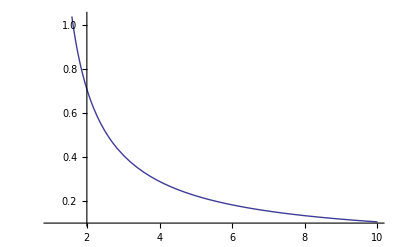

```mathematica
Plot[r[n],{n,1,10}]
```